# Alkali atom magnetic field shifts and branching ratios

The math presented here relies heavily on https://steck.us/alkalidata/cesiumnumbers.1.6.pdf

#### Declare constants

```mathematica
ℏ = 1; 
h = 2*Pi*ℏ; 
μB = 1.399624604; 
(* Cesium 133 values 

gI = -0.00039885395; 
gJGs = 2.00254032; 
gJEs = 1.334; 
totIGs = 7/2; 
totIEs = 7/2; 
totJGs = 1/2; 
totJEs = 3/2; 
AhfsGs=2.2981579425  10^3; (* in MHz *)
BhfsGs=0;
ChfsGs=0;
AhfsEs=50.28827; (* in MHz *)
BhfsEs=-0.4934 ; (* in MHz *)
ChfsEs=0.560 10^-3;(* in MHz *)

End Cs 133 values *)

(* Li 6 values *)

gI = 0.0004476540; 
gJGs = 2.0023010; 
gJEs = 1.335; 
totIGs = 1; 
totIEs = 1; 
totJGs = 1/2; 
totJEs = 3/2; 
AhfsGs=152.1368407; (* in MHz *)
BhfsGs=0;
ChfsGs=0;
AhfsEs=-1.155; (* in MHz *)
BhfsEs=-0.10 ; (* in MHz *)
ChfsEs=0;(* in MHz *)

(* End Li 6 values *)
```

#### Solve ground state

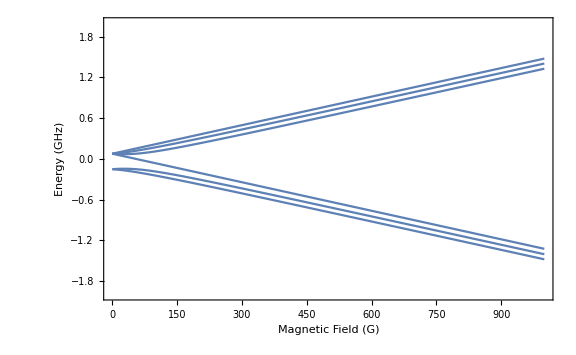

```mathematica
nStatesGs=(2totIGs+1)*(2totJGs+1);
IzGs=DiagonalMatrix[Table[mi,{mi,-totIGs,totIGs}]];
JzGs=DiagonalMatrix[Table[mj,{mj,-totJGs,totJGs}]];
IplusGs=DiagonalMatrix[Table[√(totIGs(totIGs+1)-mi(mi+1)),{mi,-totIGs,totIGs-1}],-1];
IminusGs=Transpose[IplusGs];
JplusGs=DiagonalMatrix[Table[√(totJGs(totJGs+1)-mj(mj+1)),{mj,-totJGs,totJGs-1}],-1];
JminusGs=Transpose[JplusGs];
JxGs=1/2(JplusGs+JminusGs);
JyGs=1/(2I)(JplusGs-JminusGs);
IxGs=1/2(IplusGs+IminusGs);
IyGs=1/(2I)(IplusGs-IminusGs);
JidGs=IdentityMatrix[2totJGs+1];
IidGs=IdentityMatrix[2totIGs+1];
OpOuter[a_,b_]:=Flatten[Outer[Times,a,b],{{1,3},{2,4}}];
IzGs=OpOuter[JidGs,IzGs];
JzGs=OpOuter[JzGs,IidGs];
IxGs=OpOuter[JidGs,IxGs];
JxGs=OpOuter[JxGs,IidGs];
IyGs=OpOuter[JidGs,IyGs];
JyGs=OpOuter[JyGs,IidGs];
HhfsSimpleGs=AhfsGs(IxGs.JxGs+IyGs.JyGs+IzGs.JzGs);
HhfsHigherOrderGs=If[Abs[BhfsGs]>0,BhfsGs((3(IxGs.JxGs+IyGs.JyGs+IzGs.JzGs)^2+3/2(IxGs.JxGs+IyGs.JyGs+IzGs.JzGs)-totIGs(totIGs+1)totJGs(totJGs+1))/(2totIGs(2totIGs-1)totJGs(2totJGs-1)))+ChfsGs(10(IxGs.JxGs+IyGs.JyGs+IzGs.JzGs)^3+20(IxGs.JxGs+IyGs.JyGs+IzGs.JzGs)^2+2(IxGs.JxGs+IyGs.JyGs+IzGs.JzGs)(totIGs(totIGs+1)+totJGs(totJGs+1)+3-3totIGs(totIGs+1)totJGs(totJGs+1))-5totIGs(totIGs+1)totJGs(totJGs+1))/(totIGs(totIGs-1)(2totIGs-1)totJGs(totJGs-1)(2totJGs-1)),0];
HzeemanGs=μB(gJGsJzGs+gIIzGs)Bz;
{evalsGs,evecsGs}=Eigensystem[HzeemanGs+HhfsSimpleGs];
evecsGs=Simplify[Table[evecsGs[[ii]]/Sqrt[Total[Conjugate[evecsGs[[ii]]].evecsGs[[ii]]]],{ii,1,nStatesGs}],Bz∈Reals];
energiesGs=Simplify[Table[Conjugate[evecsGs[[ii]]].(HzeemanGs+HhfsSimpleGs+HhfsHigherOrderGs).evecsGs[[ii]],{ii,1,nStatesGs}],Bz∈Reals];
mIlistGs=Table[IzGs[[ii,ii]],{ii,1,nStatesGs}];mJlistGs=Table[JzGs[[ii,ii]],{ii,1,nStatesGs}];FlistGs=Flatten[Table[Table[F,{mF,-F,F}],{F,totIGs-totJGs,totIGs+totJGs}]];mFlistGs=Flatten[Table[Table[mF,{mF,-F,F}],{F,totIGs-totJGs,totIGs+totJGs}]];mImJtoFmFGs=Quiet[Transpose[Table[Flatten[Table[Table[ClebschGordan[{totIGs,mIlistGs[[ii]]},{totJGs,mJlistGs[[ii]]},{F,mF}],{mF,-F,F}],{F,totIGs-totJGs,totIGs+totJGs}]],{ii,1,nStatesGs}]]];evecsHighFieldGs=Chop[N[evecsGs/.Bz->10^10],10^-4];
evecsLowFieldGs=Chop[N[evecsGs/.Bz->0],10^-4];
IJcomponentsGs[vec_]:=Module[{max,indmax},
	indmax=Ordering[Abs[vec],-1][[1]];
	{mIlistGs[[indmax]], mJlistGs[[indmax]]}
];
FmFcomponentsGs[vec_]:=Module[{max,indmax,FmFvec},
	FmFvec=mImJtoFmFGs.vec;indmax=Ordering[Abs[FmFvec],-1][[1]];{FlistGs[[indmax]],mFlistGs[[indmax]]}];
{mIhighfieldGs,mJhighfieldGs}=Transpose[Table[IJcomponentsGs[evecsHighFieldGs[[ii]]],{ii,1,nStatesGs}]];
{FlowfieldGs,mFlowfieldGs}=Transpose[Table[FmFcomponentsGs[evecsLowFieldGs[[ii]]],{ii,1,nStatesGs}]];
evecsFmFGs=Table[mImJtoFmFGs.evecsGs[[ii]],{ii,1,nStatesGs}];
(*Plot[energiesGs*10^-3,{Bz,0,15000},ImageSize->Large,Frame->True,FrameLabel->{"Magnetic Field (G)","Energy (GHz)"},PlotRange->{{0,15000},{-25,25}}]*)
Plot[energiesGs*10^-3,{Bz,0,1000},ImageSize->Large,Frame->True,FrameLabel->{"Magnetic Field (G)","Energy (GHz)"},PlotRange->{{0,1000},{-2,2}}]
```

```mathematica
Differences[Sort[energiesGs/.Bz->892]]
```

{75.229,80.276,2352.43,76.3467,72.1414}

```mathematica
155.501-75.229
```

80.272

#### Solve excited state

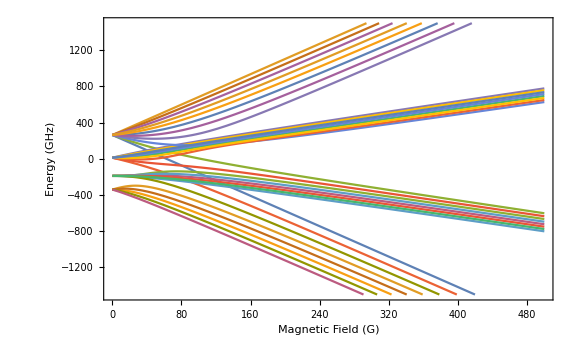

```mathematica
nStatesEs=(2totIEs+1)*(2totJEs+1);
IzEs=DiagonalMatrix[Table[mi,{mi,-totIEs,totIEs}]];
JzEs=DiagonalMatrix[Table[mj,{mj,-totJEs,totJEs}]];
IplusEs=DiagonalMatrix[Table[√(totIEs(totIEs+1)-mi(mi+1)),{mi,-totIEs,totIEs-1}],-1];
IminusEs=Transpose[IplusEs];
JplusEs=DiagonalMatrix[Table[√(totJEs(totJEs+1)-mj(mj+1)),{mj,-totJEs,totJEs-1}],-1];
JminusEs=Transpose[JplusEs];
JxEs=1/2(JplusEs+JminusEs);
JyEs=1/(2I)(JplusEs-JminusEs);
IxEs=1/2(IplusEs+IminusEs);
IyEs=1/(2I)(IplusEs-IminusEs);
JidEs=IdentityMatrix[2totJEs+1];
IidEs=IdentityMatrix[2totIEs+1];
OpOuter[a_,b_]:=Flatten[Outer[Times,a,b],{{1,3},{2,4}}];
IzEs=OpOuter[JidEs,IzEs];
JzEs=OpOuter[JzEs,IidEs];
IxEs=OpOuter[JidEs,IxEs];
JxEs=OpOuter[JxEs,IidEs];
IyEs=OpOuter[JidEs,IyEs];
JyEs=OpOuter[JyEs,IidEs];
HhfsSimpleEs=AhfsEs(IxEs.JxEs+IyEs.JyEs+IzEs.JzEs);
HhfsHigherOrderEs=If[Abs[BhfsEs]>0,BhfsEs((3(IxEs.JxEs+IyEs.JyEs+IzEs.JzEs)^2+3/2(IxEs.JxEs+IyEs.JyEs+IzEs.JzEs)-totIEs(totIEs+1)totJEs(totJEs+1))/(2totIEs(2totIEs-1)totJEs(2totJEs-1)))+ChfsEs(10(IxEs.JxEs+IyEs.JyEs+IzEs.JzEs)^3+20(IxEs.JxEs+IyEs.JyEs+IzEs.JzEs)^2+2(IxEs.JxEs+IyEs.JyEs+IzEs.JzEs)(totIEs(totIEs+1)+totJEs(totJEs+1)+3-3totIEs(totIEs+1)totJEs(totJEs+1))-5totIEs(totIEs+1)totJEs(totJEs+1))/(totIEs(totIEs-1)(2totIEs-1)totJEs(totJEs-1)(2totJEs-1)),0];
HzeemanEs=μB(gJEs JzEs+gI IzEs)Bz;
{evalsEs,evecsEs}=Eigensystem[HzeemanEs+HhfsSimpleEs];
evecsEs=Simplify[Table[evecsEs[[ii]]/Sqrt[Total[Conjugate[evecsEs[[ii]]].evecsEs[[ii]]]],{ii,1,nStatesEs}],Bz∈Reals];
energiesEs=Simplify[Table[Conjugate[evecsEs[[ii]]].(HzeemanEs+HhfsSimpleEs+HhfsHigherOrderEs).evecsEs[[ii]],{ii,1,nStatesEs}],Bz∈Reals];
mIlistEs=Table[IzEs[[ii,ii]],{ii,1,nStatesEs}];mJlistEs=Table[JzEs[[ii,ii]],{ii,1,nStatesEs}];FlistEs=Flatten[Table[Table[F,{mF,-F,F}],{F,totIEs-totJEs,totIEs+totJEs}]];mFlistEs=Flatten[Table[Table[mF,{mF,-F,F}],{F,totIEs-totJEs,totIEs+totJEs}]];mImJtoFmFEs=Quiet[Transpose[Table[Flatten[Table[Table[ClebschGordan[{totIEs,mIlistEs[[ii]]},{totJEs,mJlistEs[[ii]]},{F,mF}],{mF,-F,F}],{F,totIEs-totJEs,totIEs+totJEs}]],{ii,1,nStatesEs}]]];evecsHighFieldEs=Chop[N[evecsEs/.Bz->10^10],10^-4];
evecsLowFieldEs=Chop[N[evecsEs/.Bz->0],10^-4];
IJcomponentsEs[vec_]:=Module[{max,indmax},
	indmax=Ordering[Abs[vec],-1][[1]];
	{mIlistEs[[indmax]], mJlistEs[[indmax]]}
];
FmFcomponentsEs[vec_]:=Module[{max,indmax,FmFvec},
	FmFvec=mImJtoFmFEs.vec;indmax=Ordering[Abs[FmFvec],-1][[1]];{FlistEs[[indmax]],mFlistEs[[indmax]]}];
{mIhighfieldEs,mJhighfieldEs}=Transpose[Table[IJcomponentsEs[evecsHighFieldEs[[ii]]],{ii,1,nStatesEs}]];
{FlowfieldEs,mFlowfieldEs}=Transpose[Table[FmFcomponentsEs[evecsLowFieldEs[[ii]]],{ii,1,nStatesEs}]];
evecsFmFEs=Table[mImJtoFmFEs.evecsEs[[ii]],{ii,1,nStatesEs}];
Plot[energiesEs, {Bz, 0, 500}, ImageSize -> Large, 
  Frame -> True, FrameLabel -> {"Magnetic Field (G)", "Energy (GHz)"}, 
  PlotRange -> {{0, 500}, {-1500, 1500}}]
```

```mathematica
DipoleMatEl=Table[
Quiet[(-1)^(FlistGs[[ii]] - 1 + mFlistGs[[ii]])*Sqrt[2*FlistGs[[ii]] + 1]*ThreeJSymbol[{FlistEs[[jj]], mFlistEs[[jj]]}, 
       {1, q}, {FlistGs[[ii]], -mFlistGs[[ii]]}]*(-1)^(FlistEs[[jj]] + totJGs + 1 + totIGs)*
      Sqrt[(2*FlistEs[[jj]] + 1)*(2*totJGs + 1)]*SixJSymbol[{totJGs, totJEs, 1}, 
       {FlistEs[[jj]], FlistGs[[ii]], totIGs}]],{ii,1,nStatesGs},{jj,1,nStatesEs},{q,-1,1}];
BranchingRatios[EsInd_,B_]:=Module[{unnorm},
unnorm=Chop[Table[Sum[N[Abs[Sum[evecsFmFGs[[ii,kk]] evecsFmFEs[[EsInd,ll]] DipoleMatEl[[kk,ll,q]]/.Bz->B,{kk,1,nStatesGs},{ll,1,nStatesEs}]^2]],{q,1,3}],{ii,1,nStatesGs}],10^-5];
unnorm(*/Total[unnorm]*)
];
AllBranchingRatios[B_]:=Table[BranchingRatios[ii,B],{ii,1,nStatesEs}]
headersGs=Table[StringTemplate["F=`F` mF=`mF`"][<|"F"->FlowfieldGs[[ii]],"mF"->mFlowfieldGs[[ii]]|>],{ii,1,nStatesGs}];
headersEs=Table[StringTemplate["F'=`F` mF'=`mF`"][<|"F"->FlowfieldEs[[ii]],"mF"->mFlowfieldEs[[ii]]|>],{ii,1,nStatesEs}];
```

```mathematica
TableView[AllBranchingRatios[892]/0.5,Headers->{headersGs,headersEs}, ImageSize->Full,ItemSize->6,HeaderSize->7,AllowedDimensions->{nStatesGs,nStatesEs}]
```

1:eJzFlmlQU2cUhoMUUYIFW6Vg0LJNMSwtxSlJ3U4gbLJJCIIELARCayhUWyWI
ggvECgHUhlaGTRYhSFGWhgqxChVkJCWkQYKokJKGYASB0KGgYqS1P+qfO0zm
DjCeme/Xmec8Z+68893PMvpAUOwKDAZj8eoYvzrz//xXasC84XpTe/x1YZNS
6j2ybN69M0/HU90lYHXI3p5e1YjwWP6WkqDAhC2bn/GoYJ1orhN0M8ozRY2j
C3pOdX4we9Vn+b7D/7XTwk5/vQMXZkXQrvCSvvblV5ntawnYs+z+Z1Pb8z5m
TUDa2go/4nP+a18wZXKw1KtPq78uOo3hIrEAwoMh4JG8UO9rfSDBVBXCA59f
sdPD6uHXvOGzqn3F0b5a50keczyn7Csg5YQ71ujxXdR+pWjzL3F/DAPxqj+B
DjzUvKyg0qiregzOnzY6rzbsQM07ZTZUbk6hA3Wq3Hei0VYrb2G4xcAa2w8D
jyoT5LFK1L564h51mjEJVIF5haNnohC887ZjJu/FURacq8OalIXHd0KL531i
fkIbaj+rb51fQFEb9Mhu4q7nyxG8U048UUVeOHfV2GqT+DoPGKNalQhStqL2
l/l8X7bjRzmMnlSD/xXt+5dY40NBjwLPs6QqfG0Eal8YJzuPLZTAdyeUrEi2
CjXPrvxSbk4VQcMqW6cvqINa+W0QtCMiNghwL2YO1/4cCOd8m95pMe0BLPnR
qg7zBvT5Hgn1jggYhMFiRnesv0grn/5J+tUfjIWAx/BXb2q9BZbTScoBFg26
7h0cdya5ovb7xCijw2RRICk9PspUULXyV/zOCEa4QxB1weBuMw6Zr8UWscjc
JENMAZ3S7rdmT0ci5vOKpLUhRnIQcC44z9YNLbmf7eSFrxyQgEt0Uaqg+AHS
HyM/2zd7C3T505VkWSeiX7LR7VN3PgHKGWsrJqpCUO+XLMzxvFnzANpbC9nH
hiUIHnt6Xr+M5AsTG+aN1mICEP3eII3Y8mEj3IjB7r+4EclrK44mt/WnZArU
+7EGGENk1Pzt+iGP1JpR+Oyc6uiHOKFWvnXNWX+39n6487ZwBKun/b7V6aTb
vn80DB5fvq0/b7n4d8zu1XzSxZViUHRNnYvPFADt4FcuDppdMF40p3DwQL4P
hgNXnLpu2g+XOqqfhkb2LtpP9a7p1t0SAuG8vu2GeG/AJaZmrsxrg8RjZZni
zch8DZLqSsnRvdDi1OfLwfUvef5b99P/pO5VwiH7YE2iFXL+CeumHqZzCLQV
qK2ZPPT5Rlt1Eme9+/YdYE+2IsVeGkO+Z69VkFuz3YB1eHWhSIM+DzXHC6nc
QE+oej4Z0XYyGMHf4H6bESe8C47rmRCaUoHo53bfLvr6TDtk5/bQpHT096FS
IwtnOwsgbcxhZzOIEbxPici67Q4NvGxcr22K2ILou11OCS6kyWHjjYBaWmo7
ar+OhFIcaayEbDEhg3kZfZ7eFZy/x9zKgN89CZzyOr8lz4OdlDunG2oHqr77
Zru5gajn2/JeUCzMGmFS3jX/5JsJ1DxRUaJZY9wM7rq9NvRdCgRvlftR8fxL
AsS9NE8q+DwI0eeQglO98FLYcGTmhfAIF7VfY5REMNmhgCxTY5pU04Tgk3V0
zw7K6iHHUc3udulB9Kn8PevTC0KAiWdkTv2NQ+23k5cYTOYxwDGG0z3rSkLw
NlHiZzk5Kniy7qEii6/9f/MvyI8r6A==

```mathematica
(* Normalize 55 -> 44 decay and then check that whole table normalizes to 1 *)
(* Check on hydrogen atom *)
(* Check factor on zeeman term *)
(* What excited state has the highest overlap with 44? *)
```

```mathematica
EnergyDiff[GsInd_,EsInd_,B_]:=Module[{diff},
diff=(energiesEs[[EsInd]]-energiesGs[[GsInd]])/.Bz->B;
diff
];
AllEnergyDiffs[B_]:=Table[Table[EnergyDiff[ii,jj,B],{ii,1,nStatesGs}],{jj,1,nStatesEs}];
TableView[AllEnergyDiffs[892],Headers->{headersGs,headersEs}, ImageSize->Full,ItemSize->6,HeaderSize->7,AllowedDimensions->{nStatesGs,nStatesEs}]
```

1:eJwNl+kjFAoUxYVKURQREWUpS4xSlsLVUyRFQj1tKJFQloSRSIMiWZO1oSwz
Y5vBzJjB3JkWLUgqskRRspY8WVr0fDj/wP3de865G9wvOHgICwkJqSxIakEF
duLjdtIcFN9jzrpvjWggKqOslVuPDqV9v19dzwZ37eei6c/TwERt+bO7E1y8
KGNu76vOQ+WZOsJoOxmW7DsafmbXXYgZ/cZY0VSHG2Vspv7xaMA7Y+UbtlPy
IPHcv1Fpm5NhqEo7R24ZF7M69OdIvTzk/sn1VthfAAaqrx0lS2/AmconzNJ/
biJ5eVr3KlknvP3ST1tkjQD8lX0SuKZ8mPjNHk6KvgReS+7cYD27gk1ywmzV
LgGoD5wg/qDx4YNKwJZl+qcgbtHe5xsa/TGDJZZ0O1QAO5bOE4nPECQWtXa/
+hMFCYpuEvll1zHw37AYPcOHUGs3oeo+V4k6N08X/nuZhTaic067oqvx99vC
JMvpCri+JltGI7MU7NW+/aW2MzBGRi32qjgTQ4mhbqdJdHBWc29d4VAOOaNv
hpUZVWgko6ftvL8GJbkxq3Y+qoSs6v429adUmK+Seq35jY70DlnC3UdMbJw/
Nx9mzgAV5rBc7hkO2oSU29r4IzK8J/dd/lqPLqvPHso1zwLvZPt/XUmpwL45
9N9nizr8GqZE5ATzUFVLqNvegAwrK3pb9WbugKhDy3sXpXokh21WTmY2YJ7D
9mChM7mgc49H4z25DWcVljeeceGihLJYyrAcIo/wUSayJB+CKqIVClbkItl2
sxReo2EPHPYnZRVi18GCz+votZD3Nac4QZgNw5Hmj90tCtDRjfJanFaCTn1P
54/v5MLS4EiSUB8bIiXFM21n7yPblbeuVqsYR9e3lxuEcUCzAWMkFFhgSb52
3jWAjNQvieqmSlS8716bHfSDC0bUHVcaImLBVfN04p+LCQjDO21t4TT+XfpD
SXeSDx+PTEYMKvBhdnmkybfN/kAI98zRWR2Fu+zjqAdZAriz7pOvyg0+CDEU
P4re2g+R/0WEPtwQjGITidc4zgIoMr/uV1SEoCLlKSacfxXi0v8MfO+KwU/J
QqEuMg8hW0ZIclUtHVfaBSaJGbJR55mYxejuGjSyjeEMBpcDxhPNnsrTYOvw
/Mi/d6rQq3NbgO4LJmYwzwVXP66ElKzdPyvaSiGi8tObFv9qVOg0k128sB9b
poM1EkQroV3r4e9Gawp8CFFpeFfOwNQcjXVW11n42dhFuukqHcaUlWsKzuRi
j2jwCSin4do5csPiJ4VYF/Cr4Vh2LUSuno5sGmOBuvGt1QM+BZgkP6OS0F6C
hiIb3+Woc2E4s/MkPGNDXePRwSbVBzi1dsU5Y+dibN6tFxd0hgPi/fKutqIs
iDzayv6QS8bBez0B9dZUJMWsvlTdx4WJWkP5wr0kKJF3n5SlJKIr1bCHruKD
P9fWxJa28KHHizF0Zgah1VH0c4j/OQjxOSu01yYajdysZZpTBZCs86Ajz2Nh
/jb7iHva9FDqTbjFdHIYiiyyGzPaJoACe8t3atEISXrn4CWBCK2k31bi0jew
rwD7300IwMt6WmlLNQf9+NV2qzMRf/6et1tq1oAmz7YZn1iUCTbW6y1UrFJA
SOnH3KXkOtyxQivK5gkPNcRbct207sFXj1L2N3Y62H7qGhjxqcchie3qG5bw
MGKZyElUz4ExiWNEc5tbUF4q2zxF4SLBa2U63RxRT+KpmOuyfLjrbeHVJEtH
icLq4YdpLNRStskqIlejKVlE7CK3Ah73zcYfOlkKBHOwXDPFwLN6l14Mb2Zi
lutmpTlPOmR85VkZy5VD+BIN3Zsvq3CtXuQF9KpBAnl7c2tRJXRHgM2hW1To
bXGTS5NgYNKkZ5BwPxOHBtZypDYywC/jlPeSW/cwF2SNAgSl2GlgkWnYVYQ9
jrRXu1fVAnmqMLXKnQWDQVvGZaLu4yGnjF/1IxR0/vxqJDqbA2LhN/w3mbPh
isgczhsWYo1j2T/nvUtwTK0v61hXLWg9ehawLYwJFmkXU1cz8rG4O/zAt+M0
fOAliM124sLupBaNO5lcdPms8uaJOB/bLDuOXlTlYTulbU3t+XRoOhS2c9b9
FnSeaRbuC67HWK1FjzudEAWjPmH1adlwc+/+9P2qKaCmUzV22KEB0XGF7s1R
HiqM5JsoJt0FtZa7BjPrYyBm6uvbE7frUCkhTP4sY4HzrO7XdVfyQMwh8GKx
Nx3DEwa/5w2xMGtJeEHUVDWeeHVvpla6Aj5LpROzmTQgawTYTlhVYbts8etH
4UzUCp2WWS9DB5byccPoC2UwNn5kh4dqNcbJMi5n19UgskUe/3CohF8VPcbZ
nylwkJmqfMGVgUJdmeHvt7Mw5PcgfXsLHS55x8orB+Shihb19rxBKR5f/3bi
oW0RKrh+LPx9pBZ6/3Z7+lJY4H2Sb5n/XwG+MdM+bHOCgukTS3mm/RywiuXt
+Uhig9B4wtp46gM0MrPInukpRm3CmgtrNnDg3Mu/e8eRCY+uiI7mqeWj1mOp
QuJLKg4Ezh5zyuHC2mbeuqGKcIiZ7pkfeJGCs8QXotxxIj7K/hvMP8WHotHf
HaFxCEJPOna72GzFHvMG8Rmjmyj8KUWkX00Axyq+PqmaRiD0S5OGWL7oYyqr
U2p4HZujM7sPPOKDz+vERmOZhftbFXi4q8gbsnSomr1CSUhRF28bjxJAz/2n
51WEubjpW+60OCL6HH2V+zO+Af2OjSxKepYBEV1vlh2WTIbAkEarc3116GgQ
8WX9ckSX3Otn0yZzYeOse9TGqDRoMC/T7+Us5JbX0kAZRx4ysms1/hvPAkf9
pxKFXTdBRWxYYWiGiyPpMztpZxH3Oan6hvqSIUnnicGFbXQU8TRmnqWzcMPH
lrP76qvxoOJPP61rFdB+7NukuHopbF70WIotVYUnvs9lJOxhYkHefXvn/XQo
8WaW//e+DAKfUn/qjFWh5HfRXadJC/7dWymke7MSxn7uoIs7UuFt0uDADk0G
xlWPQeE8Eyc2pI37LmbAiTDTd7pb7qHM1sUXYlJK0V6D0LqfWoQqPduYRpq1
8ImoG0IJY8HJs4pqmofu49O9MVvbOBTM9nF5GVrFgQMiq52VjrBhaurLzGqx
QtTZmxN21aQE9Us9rx6arIUL+x2OaKYwgU069VzjWj6ubz5/XWQLDYe/2fgk
+3KBzSWqaI0HQO/Psiupu9Kx9MnSyF3vrqExUT2WtooP615sHDptghC5bsCs
scUDE6xdlzkr3MbLD9nSTe18aE2U6cgtQQgRbjFl5IWg4l62prj8Ddx9mjdq
GMwHgce5CqsEHgCXFhhKsoVJArHkln8Krl+s39+x4M8tb7X/Jh3kokqcHVgO
Ip66aaB//l0DPkg9Ud2ccQe81JNCNnAX+gNVq7tTux4PNuvpHyEgJr2dWduG
OXCU0L7N1S4V6P5Sjw8ubcADWd5LSGQeDr3W6STUZQLml/urXI4DaRPb8qOW
dTigSyENJCA+7a9NIFDuwe63JKeTdnSskZxrd2pm4esbibFGndU48jxsi61N
BQQsv0jfMk6DTsp1/WKdBb5ZtWyi2wK/HwN6nnp0sJQ39F1TVAbq/t7rFMWq
kZ/56LhDfg3GbP/eZ+ZXCXEU1oUtilSINS4S1djDQJMTpW5pCiw0C33TFDFM
h189m0M+tuThmYGfDadOlyK5Q11FnViEISLGK5ugFnbd39a6K4UFpXKrg4Q3
3se1s8RrtHgK/pd6atOKFxwo1JIrr/Rjg2XRe6uxdw8wfCb5+VHxErzx2qfj
0zIONAYcqaijMEHM0ElB6HA++kW4ven5Q0ULOftHaiQuDB09bfOj5zKkSBtU
kYXSUGZWetTZNRJV2UEfNI35sFgswKLfDQEEm9rdeo/gVKhP0MWCBHQVEvO1
medD7YvTBMVWBGuPQekv5YF4/fKjNPX8GNQmr9zDzOVDWt9Sd8tuHhA0OZVT
Qm5QtG9Rb9b2ZFy6O3Kn8zEBSGTof7Yc4CJ6OWzLI/Axd7+JnLIvD0sT9yrO
W6ZByDp362tr4uHBeQL/FtbjWNlWNXoY4t3WD5HCflngqs3LTvqdBN+2ytKE
cxrwyRaj4BwFxImWNRZu5zKgNSPSIupVNBz6dShNorMOr0mWhph2ILa+L5hy
dc6FUoGtqzOJjsp/eB8PiLDR9LJTCkGyBmUnxuSO95ZDnl5/tmkUDSwz9u+6
516FobGRDwMzmBgjpqR+Ya4SLppRjqiblMHtk/oaMmbVqB0b72nTUYOK1lpv
9xpVQnWLpotpJQW+a/hKricy8IFNoE+CPQvfxK8QxFTRQUkhvrVbNg+nFumM
Hl9aioRpZ9uNykVICFIJafarhSnpdSZmyAKzHf+Q/z4uwBLZsvISPQrSRK2S
V85x4ET2vBwjhw1vHq0MGg5/gBKyD6edKorRwtLRYtCQA1cHzOQbOphw1ylm
759pMs7npAh15VNxLtZQV6OKCyUZ949PVEXCrBKx43NuMqK8padg+2Vsbx/d
GUXiA1tjOMe4HAF1Xz7PyLIFTPxZ97MnFmWUrz7NtxGAz0hXfKAiH1Bpsc2M
1Rm0T3B4X9Edhb0NJPKKET5ErCQmzBkv5McoNHqIB8DakiRRLLyFHNeZO2XF
AvjwbpVspXYdUm8IXrx25KP/LQXrmzU8PB77+Ogh1VR4J+HK39wWByFlUpOz
Yg3Y3lJQN5iHaP3sVL2TbSaoWIdXNtbchodB092+nxqw8mDJyjYzRHJj2pVq
qztAuBHB2ZQYBeqmWx9f3lCPPgTFVYG/ECPbN+hXG+RAqk1U5aV7dFxCmtL3
VWKj2t8b/XaaNWj9IfqyErUcWpVDf83b0kBbOTKhIbwKXSVrpFPpTLwXOfTG
rq8SCnSBNbi4DIIHPYK3Ha3G1ZLIOve9Brfjj+ub1lfCYAPWzhMp8K48/5Rp
OgPj24rraN4sHBfp9PfMpMOXLyHHxOtzsWuooDKoi4ay75tXmUwWYr2QR7oF
qRaiyKeOMNpZsFGJ4yGXWYCJf1SDUJiCRsnx5dckuTCy6Z/tGlVs4NBIxovs
H+Dkb+M632vF2NJ696TLQQ5IXIzesfUrEyJ2/RFf85yMn6KXPfkeRF34I8P3
Zz3jwgdrT6vdItFwfI98/67gJLRn1SWvzwjAkVV3XYKpfGhyS+fqvl7I7yRB
7vhpV4h7v6Ot5BYJN7lof7lzQQCR6rFUL4sF/vQx01NrnJHAVPrMXXsVJ+f0
ecKSC/183yba15MIFw88zVlGDYYP003yfs7x2JJ9v6agSQD/AzxvMLk=

```mathematica
JmJgs[GsInd_,EsInd_,B_]:=Module[{diff},
diff=(energiesEs[[EsInd]]-energiesGs[[GsInd]])/.Bz->B;
diff
];
AllEnergyDiffs[B_]:=Table[Table[EnergyDiff[ii,jj,B],{ii,1,nStatesGs}],{jj,1,nStatesEs}];
TableView[AllEnergyDiffs[892],Headers->{headersGs,headersEs}, ImageSize->Full,ItemSize->6,HeaderSize->7,AllowedDimensions->{nStatesGs,nStatesEs}]
```